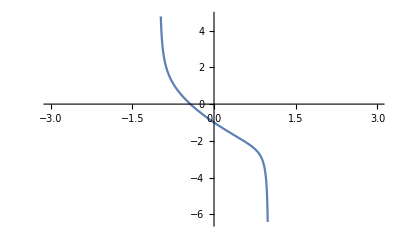

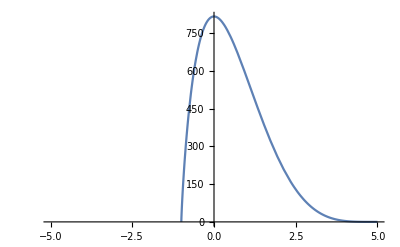

```mathematica
h=1;
m=1;
w=1;
a=1;
b=5;
n=0;
λ=Sqrt[m*w/h];
En=n+1/2+n*(n+1)/2*a^2;

Plot[LegendreP[(-h+Sqrt[h^2+8 a^2 En m+4 a^4 m^2 w^2])/(2 h),(a^2 m w)/h,x/a] +LegendreQ[(-h+Sqrt[h^2+8 a^2 En m+4 a^4 m^2 w^2])/(2 h),(a^2 m w)/h,x/a] ,{x,-3,3}]

Plot[(a+x)^(λ^2*a^2*b/(a+b))*(b-x)^(λ^2*a*b^2/(a+b))*JacobiP[n,(2*λ^2*a^2*b/(a+b)),(2*λ^2*a*b^2/(a+b)),((2*x+a-b)/(a+b))],{x,-5,5}]
```